```mathematica
me=ImageData[ColorConvert[Import["/Users/johnlewisiii/Pictures/photo3085.jpeg"] ,"Grayscale"]];
```

```mathematica
mef=ListInterpolation[me]
```

InterpolatingFunction[{{1., 296.}, {1., 280.}}, <>]

```mathematica
fme=Fourier[me];
```

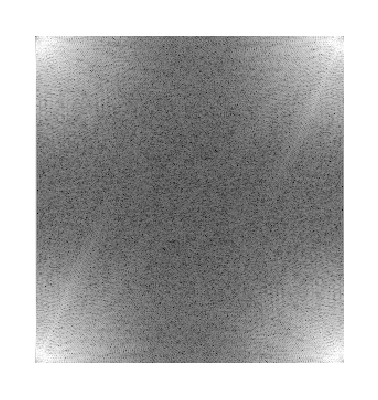

```mathematica
ArrayPlot[Log10[Abs[fme]]]
```